```mathematica
双直导线的磁力线分布——折线法
```

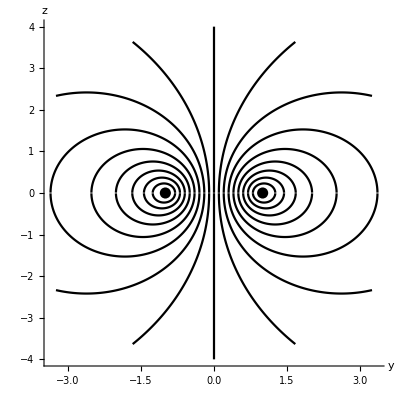

```mathematica
By[y_,z_]:=(1/((d/2-y)^2+z^2)-1/((d/2+y)^2+z^2)) z;
Bz[y_,z_]:=(d/2-y)/((d/2-y)^2+z^2)+(d/2+y)/((d/2+y)^2+z^2);
forceline={};d=2.0;r1=step=0.005;r2=2d;
Do[
θ=π/2;p={y0,r1};single={p};
While[(Abs[p[[2]]]>=r1)∧(Norm[p]<r2),
AppendTo[single,p];
p=p+step*{Cos[θ],Sin[θ]};
θ=Arg[By[p[[1]],p[[2]]]
+ⅈ*Bz[p[[1]],p[[2]]]]];
AppendTo[forceline,single];m=Length[single];single=Table[{single[[j,1]],-single[[j,2]]},
{j,m}];AppendTo[forceline,single],
{y0,-0.8×d/2,0.8×d/2,0.1×d/2}]
Show[
Graphics[{Thickness[0.004],Line/@forceline}],
Axes->True,AxesLabel->{"y","z"},
AxesStyle->Thickness[0.003],AspectRatio->1,
Epilog->{PointSize[0.02],
Point/@{{-d/2,0},{d/2,0}}}]
Clear[By,Bz]
```